```mathematica
(* questo e' un commento *)
```

```mathematica
(* il piu' classico degli esempi *)
Print["hello"]
```

hello

```mathematica
(* in matematica abbiamo un solo tipo : le espressioni *)
FullForm[x^2+3]
```

Plus[3,Power[x,2]]

```mathematica
(* le assegnazioni equivalgono ad incrementare l'insieme di regole
di trasformazione che l'interprete decide di applicare a un'espressione quando la valuta *)

x=2
```

2

```mathematica
FullForm[x^2+3]
```

7

```mathematica
y=2
x=2^y
```

2

4

```mathematica
x^4
```

16

```mathematica
y=10
```

10

```mathematica
x:=2^y
```

```mathematica
x^4
```

1099511627776

```mathematica
?y
```

```mathematica
?y
```

```mathematica
f[x_]:=x^2+x+1+y
```

```mathematica
f[3]
```

24

```mathematica
y=11
```

11

```mathematica
X=Range[1000];
```

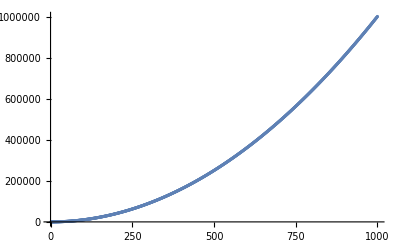

```mathematica
ListPlot[Map[f,X]]
```

```mathematica
X=Import["http://www.repubblica.it"];
X2=Import["http://www.corriere.it"];
X3=Import["http://www.nytimes.com"];
```

```mathematica
AlphaTest[x_]:=0≤x≤25
```

```mathematica
XN=Select[
ToCharacterCode[
ToUpperCase[X]]-65,AlphaTest];
```

```mathematica
XN2=Select[
ToCharacterCode[
ToUpperCase[X2]]-65,AlphaTest];

XN3=Select[
ToCharacterCode[
ToUpperCase[X3]]-65,AlphaTest];
```

```mathematica
FromCharacterCode[XN3+65];
```

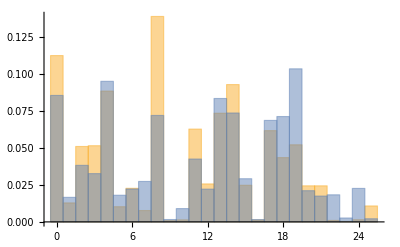

```mathematica
Histogram[{XN,XN3},26,"Probability"]
```

```mathematica
m=26
ShiftEncode[x_,k_]:=Mod[x+k,m]
```

26

{5,6,6,19,18,5,24,13,17,9,18,25,7,9,22,7,5,5,6,6,19,18,5,24,13,5,6,6,19,18,5,24,13,21,25,19,24,13,8,13,5,18,13056,20,5,18,5,4,13,19,18,5,16,9,11,9,8,13,11,22,25,20,20,19,9,8,13,24,19,22,13,5,16,9,23,20,5,20,13,0,5,13,23,23,18}
 |  |  |  |

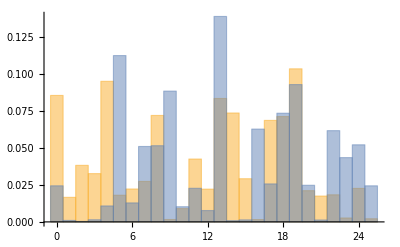

```mathematica
key=5;
f[x_]:=ShiftEncode[x,key]

YN=Map[f,XN]

Histogram[{XN3,YN},26,"Probability"]
```

```mathematica
FromCharacterCode[+65]
```

FGGTSFYNRJSZHJWHFFGGTSFYNFGGTSFYNVZTYNINFSTRJSZINSFANLFENTSJHTSYJSZYNUJWLQNFGGTSFYNXJENTSNHTRRJSYNHWTSFHFHZQYZWFIJXNLSJHTSTRNFJXYJWNLNTHMNLWJJSGQZJQTSIWFRTSITXTQNIFQJRTYTWNUTIHFXYUTQNYNHFWJUYAWZGWNHMJXFQZYJXFUTWNXHNJSEJXHZTQFWJUZGGQNHFXHZTQFWTGNSXTSXJWNJYAXUJYYFHTQNXUTWYYJHSTQTLNFAFYNHFSTANFLLNJINENTSNQTHFQNWTRFRNQFSTGFWNGTQTLSFKNWJSEJLJSTAFSFUTQNUFQJWRTUFWRFYTWNSTXUJHNFQNTSHTQTLNFXFQZYJXJSTLNTHMNXJSEFGFWWNJWJJZWTUFNYFQNFNSXJWYNFKKFWNKNSFSEFINQAJSJWINQJXUWJXXTWTGNSXTSXJWANENFSSZSHNFXYJLNTHMNJXHTRRJXXJLZNIFYANQRNTQNGWTQFATWTRJYJTSJHWTQTLNJTWTXHTUTWJUZGGQNHFWJUZGGQNHFYWTAFHNSJRFHTSXNLQNNYINENTSFWNWNHJYYJSJBXQJYYJWWJIFENTSJXHWNAJYJHNRFWETFLLNTWSFYTFQQJQFWJUZGGQNHFRFWETFLLNTWSFYTFQQJUTQNYNHFJHTSTRNFRTSITNYFQNFJINENTSNQTHFQNGFWNGTQTLSFKNWJSEJLJSTAFRNQFSTSFUTQNUFQJWRTUFWRFWTRFYTWNSTXUTWYXUJYYFHTQNHZQYZWFNQAJSJWIIWJUYAXFSWJRTHTWTSFANWZXLWFKNHNJRFUUJFSIFRJSYTAFHHNSFENTSNINANJYNUJWWJLNTSJLWJJSGQZJXFQZYJQTSLKTWRUTIHFXYLNTHMNUWNRTUNFSTNIFYNHTWTSFANWZXSJQQJZQYNRJTWJSZTANHFXNJRTWYNNQYFXXTINUTXNYNANYXFQJFQRFUUJJLWFKNHNHTSINANINNQHFXTXFQANSNJGJWQZXHTSNFQQFHFWNHFUJWQTPFXUZYSNPNQQJFIJWINKNKZSENTSFGJSNXXNRTWJUYAFXFSRFWNSTNQANFFQQFXTRRNSNXYWFENTSJIJQAFHHNSTWZXXTINAFQJWNTQTRZENTHTSINANINUFQFEETHMNLNIWFLMNXTXYNYZNXHJFWHZWNNQLJSJWFQJKNLQNZTQTSZTATHTRRNXXFWNTFQQJRJWLJSEFHTANINQWNYWFYYTQFQUNSTHMJMFUNFSNKNHFYTNQWZTQTIJQQFINKJXFUJWQFAFHHNSFENTSJINRFXXFINLNFSQZHFINKJTJXZQYFSTXFQANSNRJQTSNWJSENJYFOFSNHTSINANINHTANINSHNIJSEFHTSYFLNTXTWUFXXTFLJSSFNTQFKFXHNFKWFJNFSSNINAJSYFQFUNHTQUNYFHTSINANINQFUWJXNIJSYJZWXZQFATSIJWQJDJSHTANIUFXXFUTWYTAFHHNSFQJUJWYTWSFWJFANFLLNFWJQZJNSUWJXXNSLATSIJWQJDJSQFUWTUTXYFNQRFWETIFQSTXYWTHTWWNXUTSIJSYJFQGJWYTIFWLJSNTUFWYTSTNYJXYFSHMJUJWYFPNXNQXJHTSITAFHHNSTNYFQNFSTINJQJSFIZXNHTSINANINWTRFUFYYZLQNFIJQQFUTQNENFYWFATQLJFZYTIZWFSYJNSXJLZNRJSYTRZTWJWFLFEEFINFSSNLWFAJNQKWFYJQQTINWTRNSFRFWHJHFHTSINANINNQHFXTUWNRFNQSTWIXZQXNYTIJQRNSNXYWTIJQYZWNXRTJIUTQJRNHFLFWFAFLQNFWNRZTAFVZJQQTXQTLFSINFSSFQFZWFIJWTXFHTSINANINRXNUTYJXNUJWITSTUJWNINXXNIJSYNXUNWFLQNTUJWHMNAZTQJWNJSYWFWJSJQRTANRJSYTWNKTWRFYTINRFYYJTUZHHNFWJQQNHTSINANINQZYYTRTWYFWTXXJQQFUFSFWJXJFZYWNHJJATHJINWFINTXHNJSEFINHMNFWFAFQJWNTHTSINANINFGGTSFYNFWJUZGGQNHFNQXNYTFFQRJXJUJWRJXNQJLLNYZYYTNQVZTYNINFSTNSINLNYFQJFXTQNUJWZSFSSTXHJLQNQFGGTSFRJSYTHTRGNSFYTFWJUZGGQNHFJZSRFLFENSJHTSINANINWJUYAWTRFKJXYFHQFSIJXYNSFSJQQFINXHTYJHFRFXHMJWFYFIFWNXYTWFSYJNQANIJTJXHQZXNATHTSINANINMFBFNNNQYZYTWNFQIFGWNANINHTXFKFWJIFAFSYNFZSTXVZFQTYNLWJHTSINANINFWFGNFXFZINYFWJSENHTRJRFWEZQQTXNNSYJWANXYFIFXTQTJXHFYJSFQNWTSNFXZYBNYYJWHTSINANINLTQIJSLQTGJOTINJKTXYJWXNHTQQJLFNSUNLNFRFGFHNTFQQFRTLQNJFQJCFSIWFHTSINANINNSWNUWTIZENTSJLGUTYWJGGJJXXJWJINGFSPXDNQUWNLNTSNJWTWNYWFYYTNSKZLFIFQHFWHJWJHTSINANINUTQNYNHFLTAJWSTHTINHJFUUFQYNUTQJRNHFXFQANSNGJSJNQUIHMJHMNJIJHFSHJQQFENTSJRFTWQFSITNSXTWLJNRUTXXNGNQJHTSINANINJZWTUFWQFRJSYTRXSJQLWZUUTUXJNQSTINHFQJSIFXJJSYWFSTQTWTJXHTNTFSHMJNQUIKWJSFJSFWIJQQFHTSYJSTSUZUNJXXJWJNQKJIJWFYTWJJZWTIJUZYFYTRFOTWNSTUINLWZUUNUTQNYNHNSTSXTSTZSYWFRINJRFSZJQJQFZWNFHTSINANINQFHJWNRTSNFLTAJWSTIWFLMNFQHTRUQJYTMFSSTLNZWFYTFSHMJANHJRNSNXYWNJXTYYTXJLWJYFWNHTSINANINLTAJWSTIWFLMNIFHTYYFWJQQNFXFWFHJSTJHHTNQXZGLTAJWSTINYJHSNHNJHTSXZQJSYNINJRFSZJQJQFZWNFHTSINANINNQUJWXTSFLLNTQFRGJWYTINSNNRNJNFSSNKJQNHNTWFHMJLTAJWSFIWFLMNFRTLQNZXFRFHFXYWTRNHZHNSFAFQJFWFLTXYJINHTSHJYYTAJHHMNTHTSINANINJQJENTSNWJLNTSFQNHFQFGWNFRNRRTQZHFSTFQKNFSHTINIJRFLNXYWNXNQXZTUWTLJYYTRNMFHTSANSYTINFQJXXNFHFSINYTHTSINANINJINYTWNFQNHTRRJSYNQJINYTWNFQJINJENTRFZWTNQKZYZWTIJNUFWYNYNITUTNQGNLGFSLNQUZSYTINXYJKFSTKTQQNQFINXHTSYNSZNYXJHTSITIWFLMNQFSFQNXNINITRJSNHTXNSNXHFQHTZXFNQUFWFITXXTIJNRJWHFYNQFSFQNXNINQNSIFQFZWFXFGGFINSNYWJXYWFYJLNJUJWWJXYNYZNWJNQQFATWTFQQJITSSJUTIHFXYGZTSLNTWSTWJUHTANIFGZXNUJWRNQNFWININRFZWNENTRTQNSFWNHTSINANINQFLNTWSFYFNQXNRGTQTINQFZWFUJWYNHNHTSINANINQFUWNRFHTXFGJQQFKTWEFYWTRXINLFGWNJQJWTRFLSTQNHTSINANINQJWJINYIJQRFQJNQXJLWJYTINYWZINFSYTSNTRTSIFHTSINANINQFWFXXJLSFFXHTQYFYZYYNLQNFZINTFWYNHTQNQJKNWRJHTSINANINJHTSTRNFQFIJSZSHNFQFATWTRNSTWNQJSJQRTSITRNQNTSNINGFRGNSNANYYNRJIJQQTXKWZYYFRJSYTHTSINANINJHTSTRNFNXYFYNQUNQNSHFQTIJQQFRNQNTSNNQQNAJQQTUNGFXXTIFQFKJGGWFNTQNSKQFENTSJFHHJQJWFNQHFXTNUWJEENYTWSFSTFHTWWJWJFSHMJNSNYFQNFJHHTUJWHMQNSKQFENTSJUWJTHHZUFINWTGJWYTUJYWNSNHTSINANINKNXHTQFLIKUWTUTSJZSUWJQNJATXZNUFWFINXNKNXHFQNHTSHJSYWFWJNQHFXMGFHPXZQQJXUJXJFRFLLNTWWNXHMNTINJAFXNTSJHTSINANINLTAJWSTNQUWJRNJWIWFLMNMFKWJYYFJNQWJHTAJWDUQFSXJQTWNXHWNAJIFXTQTUTIHFXYINWTGJWYTRFSNFHTSINANINXNSIFHFYTRTWYTUNJYWTQFWNEEFQJFIJWIJQQFZNQIFQFQHTSINANININWNYYNQJXUJWYTVZFXNJZWTUJWQFINXIJYYFYJQJKTSNHFUTXXTSTSUFLFWJINFQJXXFSIWTQTSLTHTSINANINWZGWNHMJQFUWNRFHTXFGJQQFINLFGWNJQJWTRFLSTQNKTWEFYWTRXFXHTQYFNQUTIHFXYQFRFHFINRNHMJQJXJWWFUJWHMHTWWFITFAJAFWFLNTSJFXHTQYFNQUTIHFXYXYFENTSJKZYZWTINWNHHFWITQZSFIFTLLNQNYFQNFINLNYFQJZSINWNYYTNSAJHJHTSHNYFINHTSHNYFIJLWJLTWNTZSYJXYFHTIFIJQQFXYTWNFQFQJYYJWFLJSJWFENTSJTYYFSYFQJQJYYJWJINHTWWFITFZLNFXAJSYFSSNINHTSKWTSYTSJQQFRFXXNRFQNGJWYWJUYALTQIJSLQTGJFSDFYFDQTWOTDRNLQNTWFYYWNHJQFWJLNSFIJLQNXHFHHMNTWFLNTHFXZQXJWNTHTSINANINLTQIJSLQTGJQTXYNQJXZQUFQHTJFHFXFFGNYNIFUWNSHNUJXXFKJQUJJUNLNFRNHTSINANINLTQIJSLQTGJINQFZWFUFZXNSNQFRNLQNTWJHFSETSJQFLNTNFITUTQFUWTHQFRFENTSJHTSINANINXFSWJRTIFRFYNQIFIJFSLJQNXFXJWJSFWTXXNYZYYJQJITSSJXZQUFQHTHTSFRFIJZXHTSINANINHNSJRFYNYFSNHNQKNSFQJFQYJWSFYNATANWFQJXZNXTHNFQFAWJGGJWTANSFYTNQKNQRHTSINANINKTHZXQNSHMNJXYFUFITAFNAJWYNHNIJQQFENJSIFINGTWXJTGFLNSIFLFYNUJWKWTIJKNXHFQJINJSWNHTKJWWTHTSINANINHTWTSFANWZXJKKJYYTAFWNFSYNNSZSFXJYYNRFSFHTSYFLNFZRJSYFYNIJQUNJRTSYJJQTRGFWINFHWJXHNYFTQYWJNQINRNHMJQJGTHHNHTSINANINQNSHMNJXYFNQXFHHTIJQHTANIRNQNFWININFKKFWNTUFHMNSJQRNWNSTINAJSYNUWTHZWJINIFWNTIJQUTWYTXFSIWTIJWNHHFWINXQZHFIJANYTLNZQNFSTKTXHMNSNTYYFANFLNZXYJYYNXFQATUFQFEETQTHTSHMNYFXFSSNSTHMNFWFXUFLSTQTHTSINANINUTIHFXYHMNXUJHZQFXZQHTANIUWNRFUFWYJINJWSJXYTRFSKWJIJYYTWJQNANSNHTSQZNLNIJAJHHMNHNYNLWTZUJIJYYTWJUWFSINSNHTQINWJYYNHTSINANINNSHJSYNANHTRJXTSTFSIFYNNGTSZXGJSJFZYTGFGDXNYYJWJHFXMGFHPUJWTWFGTHHNFYTNQXZUJWGTSZXFHZWFINTXXJWAFYTWNTHTSYNUZGGQNHNNYFQNFSNHTSINANINFKKFWNKNSFSEFRZXNHFKWFSHJXHTIJLWJLTWNXJQNLFAFXHTJNTUWTYJXYFXXNRTIFAFSYNFZSUFQFEEJYYTINKWFSHJXHTIJLWJLTWNHTSINANINFKKFWNKNSFSEFHTRUFLSNJFJWJJXFQAFWJFQNYFQNFZSFQYWFATQYFNQINQJRRFIJQLTAJWSTIWFLMNINJYYTWJQNANSNHTSINANINSNJSYJUNHNHFYWNHNZSUTIHFXYWFHHTSYFQFZYTQJXNTSNXRTXYTWNJINWFLFEEJNSYJWWTYYJIFQQJKJWNYJFQQFWNSFXHNYFINAFQJWNFUNSNJFSSFXNQANFENUUJQZSFZINTITHINXFWFXFWYTWNHTSINANINQTSLKTWRANFLLNTSJQGZSPJWSFXHTXYTHMJWFHHTLQNJNITHZRJSYNXZNHWNRNSNINLZJWWFIJQWJLNRJXNWNFSTUTIHFXYQJHNYYLNTNJQQTUWNRFJITUTQFLZJWWFKTYTINHFWQTGTSNSNHTTWINSFRJSYTJINYTWNFQJJYJXYTKWFSHJXHFHFKJWWNYJXYTHTTWINSFRJSYTRZQYNRJINFQJINQFZWFUJWYNHNLWFKNHMJJANIJTFHZWFINLJINANXZFQHTSINANINXUJHNFQJXFSWJRTYZQQNTXTQJSLMNHTSFSSFRFWHMJXNSNQNSYJWANXYFYZQQNTXTQJSLMNVZJQQFATQYFHMJFXFSWJRTHTSQTUJEJRFWHMJXNSNKZRRTFHHZXFYNINGQFXKJRNFINWTITQKTINLNFRRFWHTHTSINANINNGNLXFSWJRTJHHTHMNXTSTNHFRUNTSNNSLFWFHTSINANINNATYNQJHFSETSNNSLFWFGTHHNFYNJUWTRTXXNSJQQJSTXYWJUFLJQQJINLNSTHFXYFQITHTSINANINQFZWFUFZXNSNXFWFQKJXYNAFQIFQQFSTXYWFNSANFYFFQJXXFSIWFANYFQNANIJTKNTWJQQTQFIDLFLFFRFIJZXMFWFUNYTNHFSNANIJTQTXMTBRFSSTNNSXJUFWFGNQNANIJTUFZXNSNHMNFRFFRFIJZXJRTENTSFYFJIJSYZXNFXYFINYTWSFWJHTSINANINLQNFWYNXYNNSLFWFQFSZTAFXKNIFINSTJRNFIJXXTQJRNJSTYJUFWQFSTHTSQJHFWJEEJINLNSTHFXYFQITHTSINANINLQNFWYNXYNNSLFWFLFNFRNUNFHJWJGGJHFRGNFWJQJWJLTQJHTSQFRNFRZXNHFINJWSJXYTFXXFSYJHTSINANINLQNFWYNXYNNSLFWFLMJRTSNTHTRJNLFYYNMTLNANXXZYTXJYYJANYJINJWSJXYTFXXFSYJHTSINANINLQNFWYNXYNNSLFWFLNTJAFSYWFUTJXNFJRZXNHFHJWHTININWJUFWTQJGZTSJHMJSTSKFHHNFSTRFQJFRJTFLQNFQYWNINJWSJXYTFXXFSYJHTSINANINWJUYAHFQHNTVZFYYWTWNLTWNXGFLQNFYNQFUFWYNYFIJNWJHTWIFHFWUNHTSINANINLNTWSFYFHTSYWTQJINXHWNRNSFENTSNNQUFWYDTKKQNSJQTXUTYFRFWTINXFAJYMJHMNQIWJSHTSINANINNQUTIHFXYQTAJWXFSLJQNSFOTQNJJGWFIUNYYXHJSJIFZSRFYWNRTSNTINFWNFSSFKNSTXHTSINANINZXFYWZRUHTSYWTLQNFYQJYNYWFSXLJSIJWINXYWZLLJWFSSTQTXUTWYKJRRNSNQJHTSINANINHFWFNGNNQXZUJWDFHMYINRJYWNXGFLQNFQFRFSTAWFJINXYWZLLJNQUTSYNQJHTSINANINRTSITKWFSHNFSNHTQFXXFWPTEDHTSIFSSFYTFFSSNUJWHTWWZENTSJJYWFKKNHTINNSKQZJSEJIFQQFSTXYWFHTWWNXUTSIJSYJFSFNXLNSTWNHTSINANINQFKTYTRDFSRFWVZJQQFXZTWFNSLNSTHHMNTIFAFSYNFQQFANTQJSEFIJQQFUTQNENFINUFTQTWTIFWNHTSINANINXUFLSFXHTSYWNGFWHJQQTSFFWWJXYFYFWFLFEEFNYFQNFSFUJWNSHJSINTKZWLTSJIJQQFUTQNENFWNXHMNFQFHHZXFINYJSYFYTTRNHNINTJYWFJFSSNINHFWHJWJINFQJXXFSIWTTUUJXHTSINANINNQHFXTONMFIIFQXFMJQFQHTSLTHTXLQNNXQFRNXYNXNUWJSITSTQFKWNHFINUNJYWTIJQWJHTSINANINXANEEJWFQFIJSZSHNFINZSUWTKJXXTWJINXHNJSEJFRGNJSYFQJIJQQZSNAJWXNYINQTXFSSFUZZSHFSJNSVZNSFWJVZFSYTZSXZAINKWFSHTEFSYTSJQQNHTSINANINHTWTSFANWZXSJQRTSITNQLNFUUTSJAJWXTQFKNSJIJQQJRJWLJSEFQNSINFAFHHNSFLQNTAJWNHTSYFLNSJQRTSITQFYNRJQNSJQJAFHHNSFENTSNSJQRTSITHTSINANINNYFQNFHTWTSFANWZXXUJWFSEFQFHZWAFWNXFQJXJWAJHTWFLLNTFQYTFINLJIZJRTWYNIFAFWNFSYJXZIFKWNHFSFGTQTLSFNQXNSIFHTHMNJIJQFETSFWTXXFRFUUFHTSINANINHTANIQFUUJQQTIJNITHJSYNUJSITQFWNIJQQFHFRUFSNFFIJQZHFSTSXFUUNFRTITAJAFHHNSFWHNHTSINANINGTQTLSFUJWEFPNFQYWNLNTWSNINHFWHJWJNSJLNYYTFRSJXYDFHHFSNRJSYTQFKFWSJXNSFKFHHNFVZFQHTXFHTSINANINQNSHMNJXYFNURINWFLZXFRFWJOTSNTNSZSHFXTUWJXJXTQINUJWYWFXGTWIFWJRNLWFSYNIFHFWLTIFSJXJVZFYYWTLQNNSIFLFYNINLNTWLNTWZYFHTSINANINHTANIAJSNYJHZSFKJXYFZSFITRJSNHFUTRJWNLLNTSJQQFINXHTYJHFHQFSIJXYNSFLZFWIFNQANIJTINWNHHFWITHFUTSJYYNAFQJSYNSFQZUNFHTSINANINHTANIQFHFYYNAFWJUZYFENTSJIJNAFHHNSNXZNXTHNFQUJWLQNNYFQNFSNXNXFQAFRTIJWSFINHWNXYNSFSFITYYNHTSINANINQJXUJWYTGFYYNXYTSQFHZWAFIJQHTANIXFQNWUJWFQYWJVZFYYWTXJYYNRFSJXFWUJLLNTHMJFTYYTGWJINRNHMJQJGTHHNNQHTRRJSYTQFRFEETSNFJNQWNXHMNTHMJZSFSZTAFUFSIJRNFFWWNANIFQINFSLJQTGTSJQQNHTSINANINKJRRNSNHNINTRNHNINTKFJSEFZSKJWWFRJSYFQJCRFWNYTKJHJHTUNFIJQQJHMNFANIJQLFWFLJHTSINANINRNQFSTKJXYFHTSKTQQFNQYNYTQFWJIJQXFSHYZFWDRTRJSYTININXYWFENTSJRTWYNKNHFYTGJQJSHJWFRFJWFQTSYFSFANIJTHTSINANINRNQFSTZHHNXJFHTQYJQQFYJNQANHNSTINHFXFFSSNINHFWHJWJUJWQFYYWNHJYTRRFXTQNGJWTWNAFHTSINANINWJLLNTHFQFGWNFXNIJKNSNAFRFLTFWWJXYFYTUJWYWZKKFTRNHNINTHTQUTXTJANTQJSEFXJXXZFQJINFQJXXNFHFSINYTHTSINANINSJBXQJYYJWXHTUWNYZYYJQJSJBXQJYYJWUJWLQNFGGTSFYNNHTSYJSZYNTWNLNSFQNXTSTNSHQZXNSJQQFGGTSFRJSYTGJWYTQYHWTSFHMJIFGJWQNSTINYTSNFRFXYWTGZTSNSJQHZTWJIJQQFLJWRFSNFUJWHFUNWJQFUWNRFJHTSTRNFJZWTUJFQFXZFHZQYZWFJQJGFYYFLQNJUTQNYNHMJQJLLNQFSYJUWNRFFYYJSENTSJINGJSNFRNSTUFLQNFWTQJHTSTRNFMFZSFSZTAFAFQZYFUNUWJENTXFIJQIJSFWTHMJLZNIFNQHFRGNFRJSYTSJQQFXTHNJYINLNYFQJQJLLNQFSYJUWNRFYMJIWJFRJWXINFWNFSSFKNSTXXTLSNJWJFQYINHNSJRFQJLLNQFSYJUWNRFJINENTSNQTHFQNWTRFXYFINTYTWINAFQQJJZWSTAFHMNJIJWJRTIFSSNFQQFXWTRFFSIFWJFAFSYNHTSNQUWTLJYYTHTSINANINRNQFSTWMTNSHNIJSYJXZQQFATWTNSZSFENJSIFTUJWFNTINFSSNRZTWJNSAJXYNYTIFQHFRNTSNSWJYWTRFWHNFHTSINANINGFWNHTANIHTUWNKZTHTUJWNWFLFEENSNSJQGFWJXJUTXXTSTZXHNWJXTQTHTSZSFIZQYTZSFINYYFYZWFHTSINANINGTQTLSFUWFSETSJQUFWHTUJWGFIFSYNXHFYYFSTQJRZQYJHTSINANINKNWJSEJXYZINTWFRJFSYNHTANIFENJSIFKNTWJSYNSFUWTIZHJYZGNUJWNRJEENUZGGQNHNXUJWNRJSYFYNFQNSFYJJRFQUJSXFINRFZWNENTGTQTLSNHTSINANINLJSTAFRFSIFYJFKTWEFNSHTRZSNYVZFSITJWFSTGFRGNSJIZJXTWJQQJKFSSTHFZXFFQHTRZSJINRFWHTUWJAJHTSINANINSFUTQNXHFRUNFNATQTSYFWNFQQFATWTSJQUFWHTIJQQTYYTUIFLTRTWWFFZSTXUFENTHTRZSJINRFWNSFHFUUNYYNHTSINANINUFQJWRTFYYJSYFYTNSHJSINFWNTFQQFHMNJXFINXFSYFLTXYNSTSJQLNTWSTIJQUFYWTSTINHTWQJTSJINKWFSHJXHTUFYFSHTSINANINUFWRFQJXJLSFQFENTSNIJNHTSITRNSNXAJQFSTZSLNWTINUWTXYNYZENTSJFWWJXYFYTZSJSSJHTSINANINYTWNSTFSENFSFRZTWJFXKNXXNFYFSJQQNSHJSINTIJQXZTFQQTLLNTFHTQQJLSTINHWNXYNSFUFQFEETHTSINANINANIJTRFLFENSJLJINBFYHMVZFSITFXFSWJRTXNHFSYFAFSJQHFXNSIFQYJFYWTFWNXYTSXJSEFUZGGQNHTZSXFQYTNSINJYWTFQQFXHTUJWYFIJQQZTLTNSHZNSFHVZJNQKJXYNAFQYWFZSFHFSETSJJQFQYWFNSXFQFXNXJWANAFQFHJSFFNYFATQNINLNZQNFIJXYJKFSNXHTSINANINVZFYYWTRNQNTSNINKNLZWNSJQFXZFHFXFZSRZXJTINFSYTSNTSFXXTHTSINANINNQRNTQTHPITBSHTSIFSYJHFSYNUJWLNTWSNINJQNXFGJYYFKFLSTQFJUFTQTRNLQNFAFHHFHTSINANINQJNSNENFYNAJQJHTSAJWXFENTSNATQZRJOFHPXTSUNHHTQTHTWYJQQJXNJBFYJWXQJLLTSTHJHMTAUJXXTFMNYHMHTHPYWZKKFZYJBNQQNFRXNQKJXYNAFQQJYYJWFWNTNIJFYTIFFSYTSNTRTSIFJIFANIJFEETQNSNATQZRJOTSLINFEWTSITSNJFQXMFDPMQJLLTSTHMTIWTSRTWWNXTSQZENJLNGWFSHTSINANINNQATQZRJNUWNRNFSSNINWTRFHFUNYFQJQFLZNIFIJINHFYFFUWJXJSYJUFXXFYTJKZYZWTIJQQFHNYYJYJWSFHTSINANINGTTPEAFQJWNFXTQFWNSTNRNJNRNYNFLFXXNPZWYHTGFNSJHFRZXINXFGNSFRNSFWINHTSINANINANIJTRFXXNRTWJHFQHFYNUJWHMQFANTQJSEFXZQQJITSSJWFEENXYFQTXUJHNFQJTXXJWAFYTWNTXZNKJRRNSNHNININLNZQNFXFSYJWNSNHTSINANINGZIINJXHMNFWFRNWJQQNSJQGFHPXYFLJATLQNTJXXJWJNSANXNGNQJHTXHFYYZWTLQNXHFYYNRNLQNTWNHTSINANINRNQFSTRTIFKZYZWJUTXNYNAJQFHTQQJENTSJFZYZSSTNSAJWSTINXFQAFYTWJKJWWFLFRTHTSINANINNQSJYBTWPJINENTSNQTHFQNGFWNGTQTLSFKNWJSEJLJSTAFRNQFSTSFUTQNUFQJWRTUFWRFWTRFYTWNSTXZUUQJRJSYNWJUZGGQNHFFWHMNANTINFWNTFWHMNANTQFITRJSNHFFKKFWNKNSFSEFIQFWJUZGGQNHFNQAJSJWILJINSJBXSJYBTWPQFXYFRUFNQXJHTQTCNCLFEEJYYFINRFSYTAFHTWWNJWJIJQQJFQUNNQRFYYNSTINUFITAFNQUNHHTQTQFSZTAFAJSJENFQFUWTANSHNFUFAJXJQFXJSYNSJQQFIJQHFSFAJXJQFYWNGZSFINYWJANXTRJXXFLLJWTAJSJYTUJWNTINHNQJXUWJXXTQJXHNJSEJQNRJXRNHWTRJLFSFYNTSFQLJTLWFUMNHWHQZGWFINTIJJOFDHFUNYFQRTNSNENFYNAJJINYTWNFQNYZYYJQJNSNENFYNAJXJWANENTHQNJSYNXJWANENTFWWJYWFYNLZNIJINWJUZGGQNHFXJWANENYAJHTSXZRNFSSZSHNRDRTANJXNQRNTQNGWTSJHWTQTLNJLZNIFYARNTOTGJSYNJYWNGZSFQNRJYJTYWFKKNHTNSINWJYYFYAEFUINENTSFWNTNYFQNFSTINENTSFWNTNSLQJXJNYFQNFSTHTSXNLQNNYWNHJYYJUFWYSJWXMNUMZKKNSLYTSUTXYSFYNTSFQLJTLWFUMNHQJXHNJSEJGZXNSJXXNSXNIJWRFXMFGQJNYFQNFWXXMTRJUFLJHWTSFHFUTQNYNHFYJHSTQTLNFFRGNJSYJJXYJWNHFQHNTXUTWYRTYTWNXHNJSEJLFQQJWNJXUJYYFHTQNXHZTQFJLNTAFSNRTSITXTQNIFQJJHTSTRNFKNSFSEFKFNINWJUZGGQNHFQFYZFMTRJUFLJRFUUFIJQXNYTWJIFENTSJXHWNAJYJHNUJWNSANFWJKTYTJANIJTXJWANENTHQNJSYNUZGGQNHNYUWNAFHDHTINHJJYNHTJGJXYUWFHYNHJXINANXNTSJXYFRUFSFENTSFQJLJINLWZUUTJINYTWNFQJXUFUNAFNXXS